## Load Data

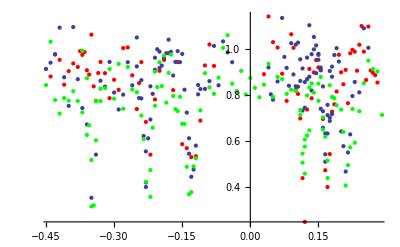

```mathematica
J1data=Drop[Import["C:\\Users\\Martin\\Documents\\Experiment\\NaK\\NaK stirap\\804\\lowerJ1data.txt","Data"],1];
J1datasc=Table[{(J1data[[i,2]]-55412)/100,J1data[[i,1]]},{i,1,Length[J1data]}];
J1verticaldata=Drop[Import["C:\\Users\\Martin\\Documents\\Experiment\\NaK\\NaK stirap\\804\\lowerJ1vertical.txt","Data"],1];
J1vertdatasc=Table[{(1200-J1verticaldata[[i,2]])/1000,J1verticaldata[[i,1]]},{i,1,Length[J1verticaldata]}];
J1horizdata=Drop[Import["C:\\Users\\Martin\\Documents\\Experiment\\NaK\\NaK stirap\\804\\lowerJ1horiz.txt","Data"],1];
J1horizdatasc=Table[{(1200-J1horizdata[[i,1]])/1000,J1horizdata[[i,2]]},{i,1,Length[J1horizdata]}];
Show[ListPlot[J1vertdatasc,PlotStyle->Red],ListPlot[J1horizdatasc],ListPlot[J1datasc,PlotStyle->Green]]
```

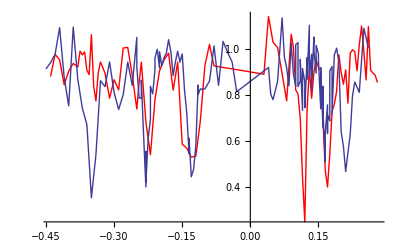

```mathematica
Show[ListLinePlot[J1vertdatasc,PlotStyle->Red],ListLinePlot[J1horizdatasc]]
```

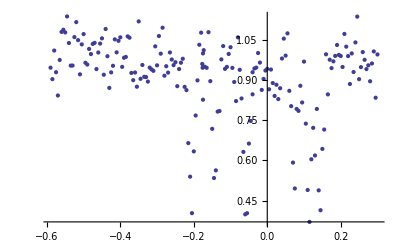

```mathematica
J1upperdata=Drop[Import["C:\\Users\\Martin\\Documents\\Experiment\\NaK\\NaK stirap\\804\\upperJ1data.txt","Data"],1];
J1upperdatasc=Table[{(J1upperdata[[i,2]]-59090)/100,J1upperdata[[i,1]]},{i,1,Length[J1upperdata]}];
ListPlot[J1upperdatasc,PlotRange->All]
```

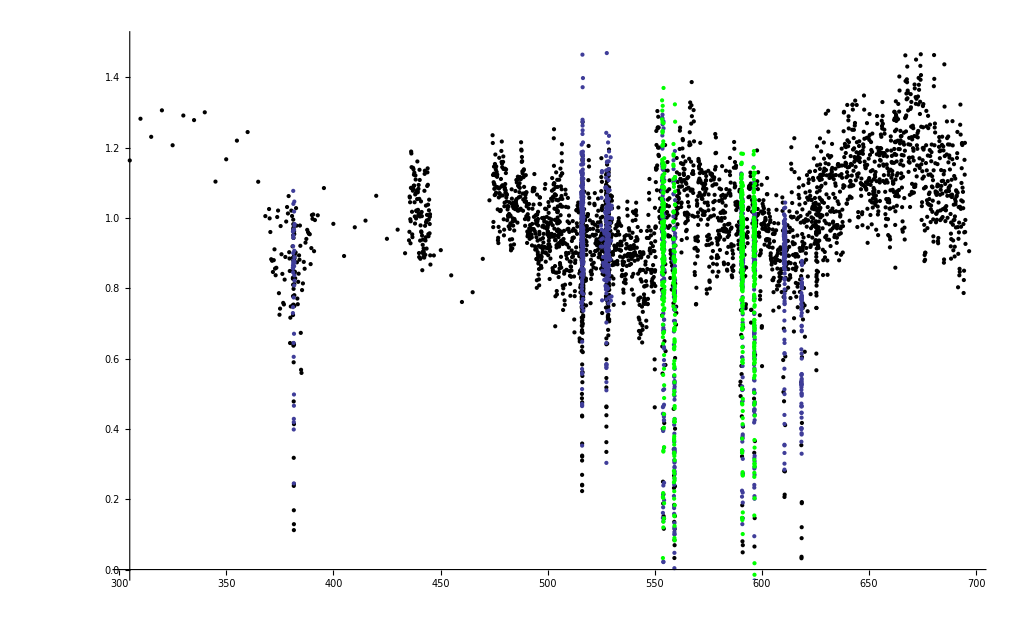

```mathematica
Broad804data=Import["C:\\Users\\Martin\\Documents\\Experiment\\NaK\\NaK stirap\\804\\BroadScan804nm.txt","Data"];
Detail804data=Import["C:\\Users\\Martin\\Documents\\Experiment\\NaK\\NaK stirap\\804\\DetailScan804nm.txt","Data"];
Detail804data372554=Import["C:\\Users\\Martin\\Dropbox (MIT)\\Experiment\\NaK\\NaK stirap\\804\\SinglePhoton_372_554THz_Norm.csv","Data"];
Detail804data372559=Import["C:\\Users\\Martin\\Dropbox (MIT)\\Experiment\\NaK\\NaK stirap\\804\\SinglePhoton_372_559THz_Norm.csv","Data"];
Detail804data372591=Import["C:\\Users\\Martin\\Dropbox (MIT)\\Experiment\\NaK\\NaK stirap\\804\\SinglePhoton_372_591THz_Norm.csv","Data"];
Detail804data372597=Import["C:\\Users\\Martin\\Dropbox (MIT)\\Experiment\\NaK\\NaK stirap\\804\\SinglePhoton_372_597THz_Norm.csv","Data"];
Show[ Show[ListPlot[Broad804data,PlotStyle->Black,PlotRange->{0,1.5}]],ListPlot[Detail804data],ListPlot[Detail804data372554,PlotStyle->Green],ListPlot[Detail804data372559,PlotStyle->Green],ListPlot[Detail804data372591,PlotStyle->Green],ListPlot[Detail804data372597,PlotStyle->Green],PlotRange->{0,1.5}]
```

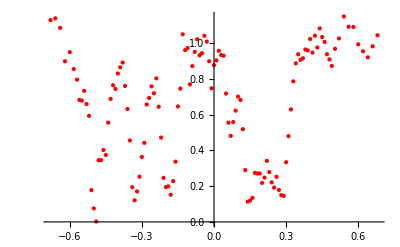

```mathematica
J1832data=Drop[Import["C:\\Users\\Martin\\Documents\\Experiment\\NaK\\NaK stirap\\832\\c3J1832.txt","Data"],1];
J1832datasc=Table[{(J1832data[[i,1]]-190.7),J1832data[[i,2]]},{i,1,Length[J1832data]}];
Show[ListPlot[J1832datasc,PlotStyle->Red]]
```

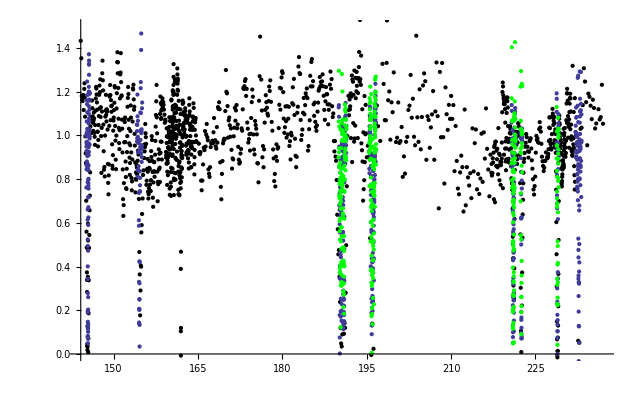

```mathematica
Detail832data=Import["C:\\Users\\Martin\\Documents\\Experiment\\NaK\\NaK stirap\\832\\Details360THzNormalized.csv","Data"];
Broad832data=Import["C:\\Users\\Martin\\Documents\\Experiment\\NaK\\NaK stirap\\832\\BroadScan360THzNormalized.csv","Data"];
Detail832data360191=Import["C:\\Users\\Martin\\Dropbox (MIT)\\Experiment\\NaK\\NaK stirap\\832\\SinglePhoton_360_191THz_Norm.csv","Data"];
Detail832data360195=Import["C:\\Users\\Martin\\Dropbox (MIT)\\Experiment\\NaK\\NaK stirap\\832\\SinglePhoton_360_195THz_Norm.csv","Data"];
Detail832data360221=Import["C:\\Users\\Martin\\Dropbox (MIT)\\Experiment\\NaK\\NaK stirap\\832\\SinglePhoton_360_221THz_Norm.csv","Data"];
Detail832data360222=Import["C:\\Users\\Martin\\Dropbox (MIT)\\Experiment\\NaK\\NaK stirap\\832\\SinglePhoton_360_222THz_Norm.csv","Data"];
Detail832data360229=Import["C:\\Users\\Martin\\Dropbox (MIT)\\Experiment\\NaK\\NaK stirap\\832\\SinglePhoton_360_229THz_Norm.csv","Data"];
Show[ Show[ListPlot[Broad832data,PlotStyle->Black,PlotRange->{0,1.5}]],ListPlot[Detail832data],ListPlot[Detail832data360191,PlotStyle->Green],ListPlot[Detail832data360195,PlotStyle->Green],ListPlot[Detail832data360221,PlotStyle->Green],ListPlot[Detail832data360222,PlotStyle->Green],ListPlot[Detail832data360229,PlotStyle->Green],PlotRange->{0,1.5}]
```

## Plot data

### 832 J=1

```mathematica
Restab832J1=Import["C:\\Users\\Martin\\Dropbox (MIT)\\Experiment\\NaK\\NaK stirap\\Singlet STIRAP\\Results832J1.dat"];
```

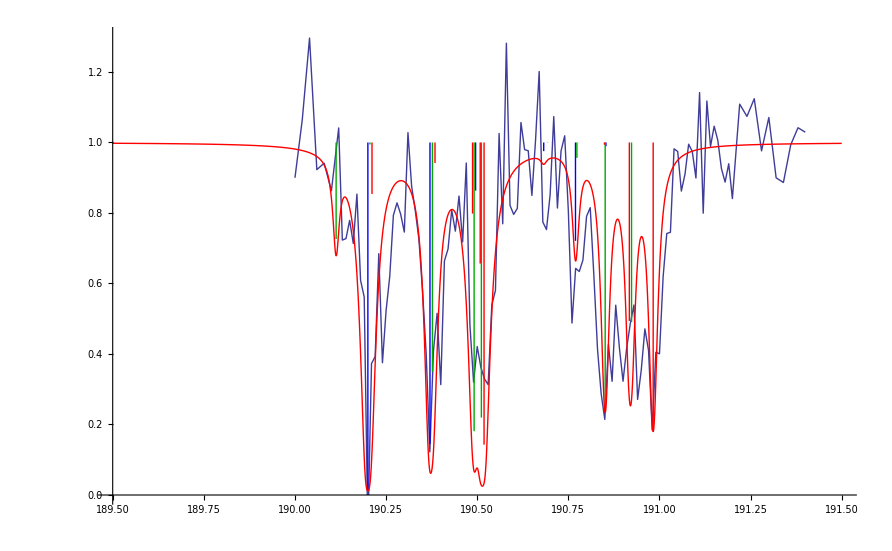

```mathematica
Show[ListLinePlot[Detail832data360191,PlotRange->{{189.5,191.5},{0,1.3}}],
Graphics[Table[{Directive[Thick,Switch[ Restab832J1[[i,3]]/2,-9/2,Blue,-7/2,Darker[Green],-5/2,Red]],Line[{{Restab832J1[[i,5]],Exp[-Restab832J1[[i,9]](Restab832J1[[i,7]]+Restab832J1[[i,8]])]},{Restab832J1[[i,5]],1}}]},{i,1,Length[Restab832J1]}]],
Plot[Exp[-Sum[Restab832J1[[i,9]]/(1+(x-Restab832J1[[i,5]])^2/Restab832J1[[i,11]]^2)*(Restab832J1[[i,7]]+Restab832J1[[i,8]]),{i,1,Length[Restab832J1]}]],{x,189.5,191.5},PlotStyle->Red,PlotRange->All],
PlotRange->{{189.5,191.5},{0,1.3}}]
```

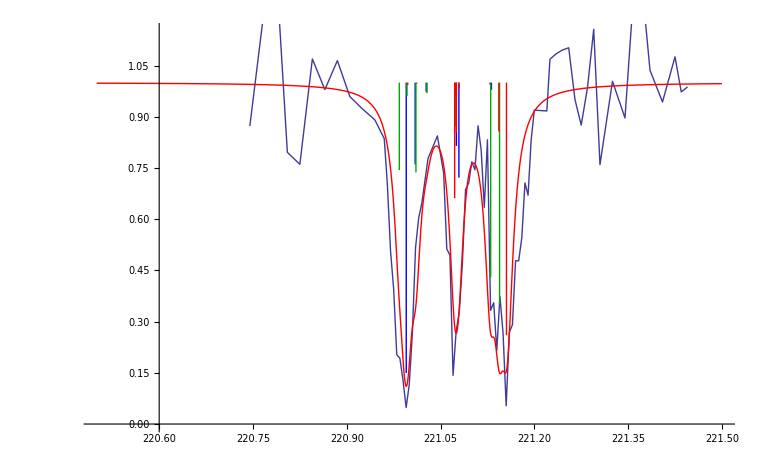

```mathematica
Show[ListLinePlot[Detail832data360221,PlotRange->{{220.5,221.5},{0,1.3}}],Graphics[Table[{Directive[Thick,Switch[ Restab832J1[[i,3]]/2,-9/2,Blue,-7/2,Darker[Green],-5/2,Red]],Line[{{Restab832J1[[i,5]],Exp[-Restab832J1[[i,9]](Restab832J1[[i,7]]+Restab832J1[[i,8]])]},{Restab832J1[[i,5]],1}}]},{i,1,Length[Restab832J1]}]],
Plot[Exp[-Sum[Restab832J1[[i,9]]/(1+(x-Restab832J1[[i,5]])^2/Restab832J1[[i,11]]^2)*(Restab832J1[[i,7]]+Restab832J1[[i,8]]),{i,1,Length[Restab832J1]}]],{x,220.5,221.5},PlotStyle->Red,PlotRange->All],
PlotRange->{{220.5,221.5},{0,1.15}}]
```

#### Copy of 832 J=1 parameters

```mathematica
B1Pi =17289.253;
BvB1Pi =0.06686421440207369;
c3 =17288.328; (*from Dunham with mass-scaling from Ferber 2000 *)
Bvc30 = 0.046723238763320296
Bvc3 = 0.046723238763320296
b3Pi = 17301.87; (*from Kowalczyk 1989 applying the isotopic shift from Dunham coefficients in my file*)
Bvb3Pi0 = 0.0633547;
Bvb3Pi = 0.0633547;
γ = 0.0024; (*Kowalczyk*)
λ0 = 0.07; (* Kowalczyk, Forbidden transitions in NaK, 1989 *)
ξBc0 = 0.16;
ξbc0 = 0.7657670034690864 (* From FCF and Ferber paper *);
BL0 =0.0035;
A=15.557 -0.0112(59+1/2);
K1Kowalczyk = 0.0104; (*J.Chem.Phys.91,2779 (1989);doi:10.1063/1.456947*)(*Same as Kato!*)
```

```mathematica
Bf0=85.7; (*Bfield in G*)
K1=Ahf1/c/100*0.84^2/2;
K2 = Ahf2/c/100*0.39^2/2; (*Kato*)
```

```mathematica
ξBc=0.27;ξbc=0.767;BL=0;γ=0;
EJ01 =17286.713;
EJ02= 17289.281;
EJ11=17288.2191;
EJ12=17289.2352;
λb=0;

Clear[Bshift,cshift,bshift,λ];
bshift[ξbc_]:=1/2 (EJ01+EJ02-√(EJ01^2-2 EJ01 EJ02+EJ02^2-8 ξbc^2))-b3Pi+A;
Bshift[ξBc_,ξbc_]:=(EJ11+EJ12+√(-4 ξBc^2+EJ11^2-2 EJ11 EJ12+EJ12^2))/2+(ξBc^2 ξbc^2)/(((b3Pi+bshift[ξbc]+2Bvb3Pi)-EJ11)((b3Pi+bshift[ξbc]+2Bvb3Pi)-EJ12)√(-4 ξBc^2+(EJ11-EJ12)^2))-B1Pi;
cshift[ξBc_,ξbc_]:=(EJ11+EJ12-√(-4 ξBc^2+EJ11^2-2 EJ11 EJ12+EJ12^2))/2+(ξbc^2 (2 ξBc^2-(EJ11-EJ12)^2+(2(b3Pi+bshift[ξbc]+2Bvb3Pi)-EJ11-EJ12) √(-4 ξBc^2+(EJ11-EJ12)^2) ))/(2 ((b3Pi+bshift[ξbc]+2Bvb3Pi)-EJ11)  ((b3Pi+bshift[ξbc]+2Bvb3Pi)-EJ12)√(-4 ξBc^2+(EJ11-EJ12)^2))-c3;
λ[ξBc_,ξbc_,γ_]:=(c3+cshift[ξBc,ξbc]-γ-1/2 (EJ01+EJ02+√(EJ01^2-2 EJ01 EJ02+EJ02^2-8 ξbc^2)))/2
Bshift[ξBc,ξbc]
cshift[ξBc,ξbc]
bshift[ξbc]
λ[ξBc,ξbc,0]
```

-0.095215

0.0103583

0.328293

-0.173974

### 832 J=2

```mathematica
Restab832J2=Import["C:\\Users\\Martin\\Dropbox (MIT)\\Experiment\\NaK\\NaK stirap\\Singlet STIRAP\\Results832J2.dat"];
```

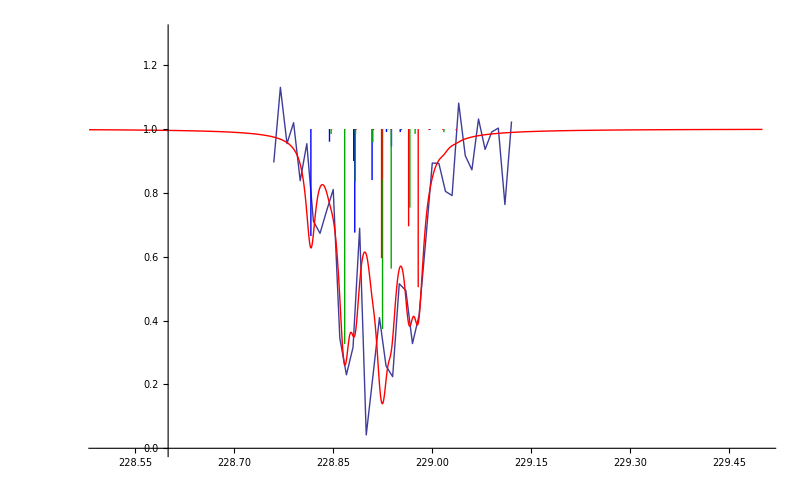

```mathematica
Show[ListLinePlot[Detail832data360229,PlotRange->{{228.5,229.5},{0,1.3}}],
Graphics[Table[{Directive[Thick,Switch[ Restab832J2[[i,3]]/2,-9/2,Blue,-7/2,Darker[Green],-5/2,Red]],Line[{{Restab832J2[[i,5]],Exp[-Restab832J2[[i,9]](Restab832J2[[i,7]]+Restab832J2[[i,8]])]},{Restab832J2[[i,5]],1}}]},{i,1,Length[Restab832J2]}]],
Plot[Exp[-Sum[Restab832J2[[i,9]]/(1+(x-Restab832J2[[i,5]])^2/Restab832J2[[i,11]]^2)*(Restab832J2[[i,7]]+Restab832J2[[i,8]]),{i,1,Length[Restab832J2]}]],{x,228,229.5},PlotStyle->Red,PlotRange->All],
PlotRange->{{228.5,229.5},{0,1.3}}]
```

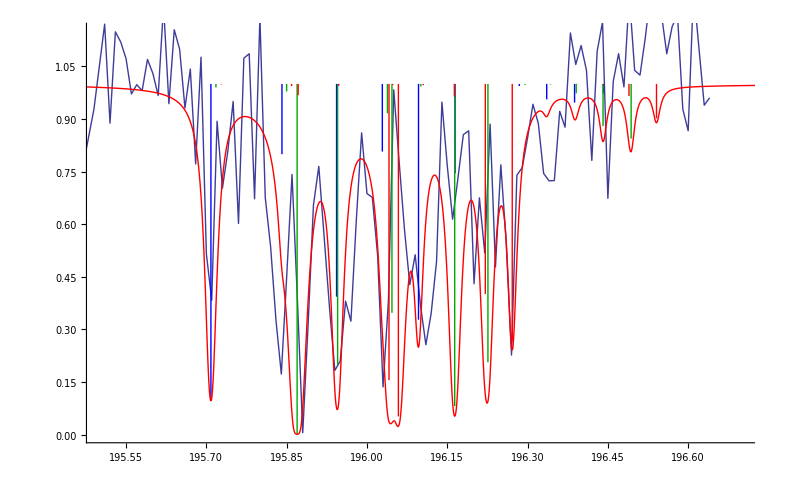

```mathematica
Show[ListLinePlot[Detail832data360195,PlotRange->{{195,197},{0,1.3}}],Graphics[Table[{Directive[Thick,Switch[ Restab832J2[[i,3]]/2,-9/2,Blue,-7/2,Darker[Green],-5/2,Red]],Line[{{Restab832J2[[i,5]],Exp[-Restab832J2[[i,9]](Restab832J2[[i,7]]+Restab832J2[[i,8]])]},{Restab832J2[[i,5]],1}}]},{i,1,Length[Restab832J2]}]],
Plot[Exp[-Sum[Restab832J2[[i,9]]/(1+(x-Restab832J2[[i,5]])^2/Restab832J2[[i,11]]^2)*(Restab832J2[[i,7]]+Restab832J2[[i,8]]),{i,1,Length[Restab832J2]}]],{x,195,197},PlotStyle->Red,PlotRange->All],
PlotRange->{{195.5,196.7},{0,1.15}}]
```

#### Copy of 832 J=2 parameters

```mathematica
B1Pi =17289.253;
BvB1Pi =0.06686421440207369;
c3 =17288.328; (*from Dunham with mass-scaling from Ferber 2000 *)
Bvc30 = 0.046723238763320296
Bvc3 = 0.046723238763320296
b3Pi = 17301.87; (*from Kowalczyk 1989 applying the isotopic shift from Dunham coefficients in my file*)
Bvb3Pi0 = 0.0633547;
Bvb3Pi = 0.0633547;
γ = 0.0024; (*Kowalczyk*)
λ0 = 0.07; (* Kowalczyk, Forbidden transitions in NaK, 1989 *)
ξBc0 = 0.16;
ξbc0 = 0.7657670034690864 (* From FCF and Ferber paper *);
BL0 =0.0035;
A=15.557 -0.0112(59+1/2);
K1Kowalczyk = 0.0104; (*J.Chem.Phys.91,2779 (1989);doi:10.1063/1.456947*)(*Same as Kato!*)
```

```mathematica
Bf0=85.7; (*Bfield in G*)
K1=Ahf1/c/100*0.84^2/2;
K2 = Ahf2/c/100*0.39^2/2; (*Kato*)
```

```mathematica
ξBc=0.27;ξbc=0.766;BL=0.0035;γ=0.0022;Nahf = 1.07; Khf=1.7;
λb=0;
EJ01 =17286.713;
EJ02= 17289.281;
EJ11=17288.2191;
EJ12=17289.2352;
Clear[Bshift,cshift,bshift,λ];
bshift[ξbc_]:=1/2 (EJ01+EJ02-√(EJ01^2-2 EJ01 EJ02+EJ02^2-8 ξbc^2))-b3Pi+A;
Bshift[ξBc_,ξbc_]:=(EJ11+EJ12+√(-4 ξBc^2+EJ11^2-2 EJ11 EJ12+EJ12^2))/2+(ξBc^2 ξbc^2)/(((b3Pi+bshift[ξbc]+2Bvb3Pi)-EJ11)((b3Pi+bshift[ξbc]+2Bvb3Pi)-EJ12)√(-4 ξBc^2+(EJ11-EJ12)^2))-B1Pi;
cshift[ξBc_,ξbc_]:=(EJ11+EJ12-√(-4 ξBc^2+EJ11^2-2 EJ11 EJ12+EJ12^2))/2+(ξbc^2 (2 ξBc^2-(EJ11-EJ12)^2+(2(b3Pi+bshift[ξbc]+2Bvb3Pi)-EJ11-EJ12) √(-4 ξBc^2+(EJ11-EJ12)^2) ))/(2 ((b3Pi+bshift[ξbc]+2Bvb3Pi)-EJ11)  ((b3Pi+bshift[ξbc]+2Bvb3Pi)-EJ12)√(-4 ξBc^2+(EJ11-EJ12)^2))-c3;
λ[ξBc_,ξbc_,γ_]:=(c3+cshift[ξBc,ξbc]-γ-1/2 (EJ01+EJ02+√(EJ01^2-2 EJ01 EJ02+EJ02^2-8 ξbc^2)))/2
Bshift[ξBc,ξbc]
cshift[ξBc,ξbc]
bshift[ξbc]
λ[ξBc,ξbc,0]
```

-0.095215

0.0103583

0.328293

-0.173974

### 804 J=1

```mathematica
Restab804J1=Import["C:\\Users\\Martin\\Dropbox (MIT)\\Experiment\\NaK\\NaK stirap\\Singlet STIRAP\\Results804J1.dat"];
```

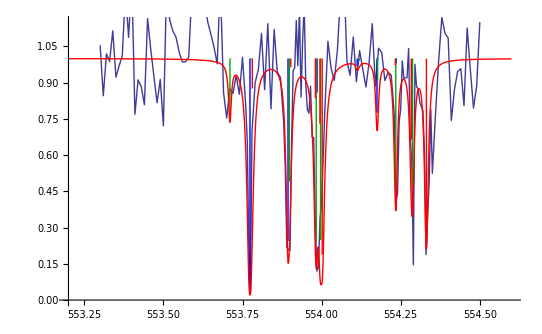

```mathematica
Show[ListLinePlot[Detail804data372554,PlotRange->{{553.2,554.6},{0,1.3}}],
Graphics[Table[{Directive[Thick,Switch[ Restab804J1[[i,3]]/2,-9/2,Blue,-7/2,Darker[Green],-5/2,Red]],Line[{{Restab804J1[[i,5]],Exp[-Restab804J1[[i,9]](Restab804J1[[i,7]]+Restab804J1[[i,8]])]},{Restab804J1[[i,5]],1}}]},{i,1,Length[Restab804J1]}]],
Plot[Exp[-Sum[Restab804J1[[i,9]]/(1+(x-Restab804J1[[i,5]])^2/Restab804J1[[i,11]]^2)*(Restab804J1[[i,7]]+Restab804J1[[i,8]]),{i,1,Length[Restab804J1]}]],{x,553.2,554.6},PlotStyle->Red,PlotRange->All],
PlotRange->{{553.2,554.6},{0,1.15}}]
```

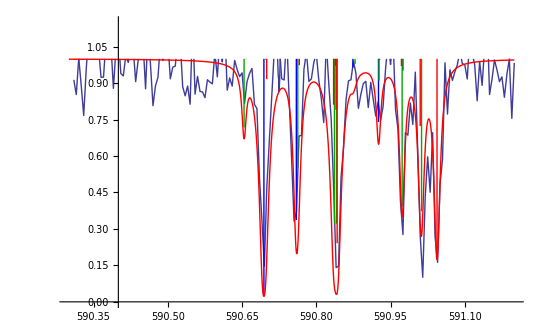

```mathematica
Show[ListLinePlot[Detail804data372591,PlotRange->{{590.3,591.2},{0,1}}],Graphics[Table[{Directive[Thick,Switch[ Restab804J1[[i,3]]/2,-9/2,Blue,-7/2,Darker[Green],-5/2,Red]],Line[{{Restab804J1[[i,5]],Exp[-Restab804J1[[i,9]](Restab804J1[[i,7]]+Restab804J1[[i,8]])]},{Restab804J1[[i,5]],1}}]},{i,1,Length[Restab804J1]}]],
Plot[Exp[-Sum[Restab804J1[[i,9]]/(1+(x-Restab804J1[[i,5]])^2/Restab804J1[[i,11]]^2)*(Restab804J1[[i,7]]+Restab804J1[[i,8]]),{i,1,Length[Restab804J1]}]],{x,590.3,591.2},PlotStyle->Red,PlotRange->All],
PlotRange->{{590.3,591.2},{0,1.15}}]
```

#### Copy of 804 J=1 parameters

```mathematica
FoundLines={c/372.61850  10^-3,c/372.61051  10^-3,c/372.59660 10^-3,c/372.59100 10^-3,c/372.55400 10^-3,c/372.55920 10^-3};
WavenumberFoundLinesAbs=Sort[1/FoundLines/10^-9/100+5211.986+61.571009321984796];
FoundLinesList=Table[{-1,WavenumberFoundLinesAbs[[v]]},{v,1,Length[WavenumberFoundLinesAbs]}];
B1J1 = 17701.534165517216;
B1J2 = 17701.757314569702;
c3N1J0=17702.50561544268;
B0c =0.03980720445338193;
B1Pi =17701.478378254094;
BvB1Pi0 =0.055787263122084596;
BvB1Pi =0.055787263122084596;
c3 =17701.35467879664;
Bvc30 = 0.03980886080387336;
Bvc3 = 0.03980886080387336;
b3Pi =17710.71202147651;
Bvb3Pi0 = 0.05489108563801892;
Bvb3Pi = 0.05489108563801892;
γ0 = 0.0124;
λ0 = 0.6;
ξBc0 = 0.582;
ξbc0 = 2;
BL0 =0.0035;
A=15.557 -0.0112(66+1/2) ;(* from Amanda Ross, Enfantin, Laser-induced fluorescence of NaK:the b(1) 3Π state, 1986 J.Phys.B:At.Mol.Phys.19 1449
(http://iopscience.iop.org/0022-3700/19/10/014) *)
```

```mathematica
Bf0=85.7; (*Bfield in G*)
K1=Ahf1/c/100*0.84^2/2;
K2 = Ahf2/c/100*0.39^2/2; (*Kato*)
```

```mathematica
BvB1Pi=BvB1Pi0;
Bvc3=Bvc30;
Bvb3Pi=Bvb3Pi0;
ξBc=0.5899; (*Note: Slight bit different value than for J=2, where it is 0.5833*)
γ=0.0215;
ξbc=.68;
λtab=λ[ξBc,ξbc,γ]
BL=0.006;
λb=0;
EJ01 =17699.3524;
EJ02= 17702.5023;
EJ11=17700.619602;
EJ12= 17701.847297;
Clear[Bshift,cshift,bshift,λ];
bshift[ξbc_]:=1/2 (EJ01+EJ02-√(EJ01^2-2 EJ01 EJ02+EJ02^2-8 ξbc^2))-b3Pi+A;
Bshift[ξBc_,ξbc_]:=(EJ11+EJ12+√(-4 ξBc^2+EJ11^2-2 EJ11 EJ12+EJ12^2))/2+(ξBc^2 ξbc^2)/(((b3Pi+bshift[ξbc]+2Bvb3Pi)-EJ11)((b3Pi+bshift[ξbc]+2Bvb3Pi)-EJ12)√(-4 ξBc^2+(EJ11-EJ12)^2))-B1Pi;
cshift[ξBc_,ξbc_]:=(EJ11+EJ12-√(-4 ξBc^2+EJ11^2-2 EJ11 EJ12+EJ12^2))/2+(ξbc^2 (2 ξBc^2-(EJ11-EJ12)^2+(2(b3Pi+bshift[ξbc]+2Bvb3Pi)-EJ11-EJ12) √(-4 ξBc^2+(EJ11-EJ12)^2) ))/(2 ((b3Pi+bshift[ξbc]+2Bvb3Pi)-EJ11)  ((b3Pi+bshift[ξbc]+2Bvb3Pi)-EJ12)√(-4 ξBc^2+(EJ11-EJ12)^2))-c3;
λ[ξBc_,ξbc_,γ_]:=(c3+cshift[ξBc,ξbc]-γ-1/2 (EJ01+EJ02+√(EJ01^2-2 EJ01 EJ02+EJ02^2-8 ξbc^2)))/2
Bshift[ξBc,ξbc]
cshift[ξBc,ξbc]
bshift[ξbc]
λ[ξBc,ξbc,0]
```

### 804 J=2

```mathematica
Restab804J2=Import["C:\\Users\\Martin\\Dropbox (MIT)\\Experiment\\NaK\\NaK stirap\\Singlet STIRAP\\Results804J2.dat"];
```

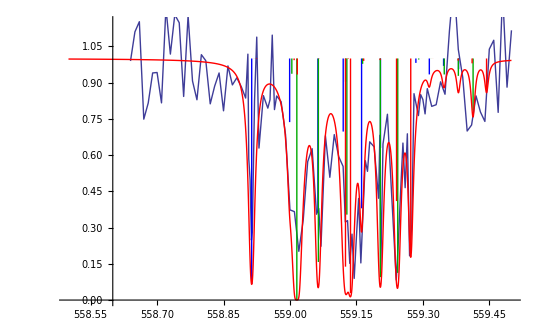

```mathematica
Show[ListLinePlot[Detail804data372559,PlotStyle->{Thick},PlotRange->{{558.5,559.5},{0,1.3}}],
Graphics[Table[{Directive[Thick,Switch[ Restab804J2[[i,3]]/2,-9/2,Blue,-7/2,Darker[Green],-5/2,Red]],Line[{{Restab804J2[[i,5]],Exp[-Restab804J2[[i,9]](Restab804J2[[i,7]]+Restab804J2[[i,8]])]},{Restab804J2[[i,5]],1}}]},{i,1,Length[Restab804J2]}]],
Plot[Exp[-Sum[Restab804J2[[i,9]]/(1+(x-Restab804J2[[i,5]])^2/Restab804J2[[i,11]]^2)*(Restab804J2[[i,7]]+Restab804J2[[i,8]]),{i,1,Length[Restab804J2]}]],{x,558.5,559.5},PlotStyle->Red,PlotRange->All],
PlotRange->{{558.5,559.5},{0,1.15}}]
```

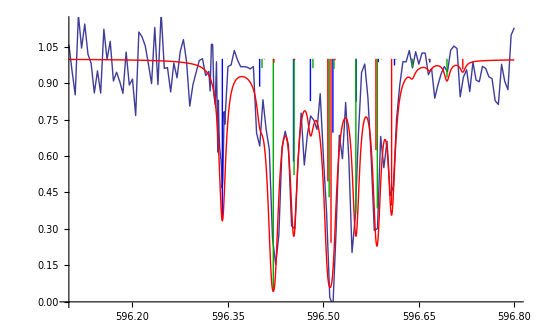

```mathematica
Show[ListLinePlot[Detail804data372597,PlotStyle->{Thick},PlotRange->{{596.1,596.8},{0,1.3}}],Graphics[Table[{Directive[Thick,Switch[ Restab804J2[[i,3]]/2,-9/2,Blue,-7/2,Darker[Green],-5/2,Red]],Line[{{Restab804J2[[i,5]],Exp[-Restab804J2[[i,9]](Restab804J2[[i,7]]+Restab804J2[[i,8]])]},{Restab804J2[[i,5]],1}}]},{i,1,Length[Restab804J2]}]],
Plot[Exp[-Sum[Restab804J2[[i,9]]/(1+(x-Restab804J2[[i,5]])^2/Restab804J2[[i,11]]^2)*(Restab804J2[[i,7]]+Restab804J2[[i,8]]),{i,1,Length[Restab804J2]}]],{x,596.1,596.8},PlotStyle->Red,PlotRange->All],
PlotRange->{{596.1,596.8},{0,1.15}}]
```

#### Copy of 804 J=2 parameters

```mathematica
FoundLines={c/372.61850  10^-3,c/372.61051  10^-3,c/372.59660 10^-3,c/372.59100 10^-3,c/372.55400 10^-3,c/372.55920 10^-3};
WavenumberFoundLinesAbs=Sort[1/FoundLines/10^-9/100+5211.986+61.571009321984796];
FoundLinesList=Table[{-1,WavenumberFoundLinesAbs[[v]]},{v,1,Length[WavenumberFoundLinesAbs]}];
B1J1 = 17701.534165517216;
B1J2 = 17701.757314569702;
c3N1J0=17702.50561544268;
B0c =0.03980720445338193;
B1Pi =17701.478378254094;
BvB1Pi0 =0.055787263122084596;
BvB1Pi =0.055787263122084596;
c3 =17701.35467879664;
Bvc30 = 0.03980886080387336;
Bvc3 = 0.03980886080387336;
b3Pi =17710.71202147651;
Bvb3Pi0 = 0.05489108563801892;
Bvb3Pi = 0.05489108563801892;
γ0 = 0.0124;
λ0 = 0.6;
ξBc0 = 0.582;
ξbc0 = 2;
BL0 =0.0035;
A=15.557 -0.0112(66+1/2) ;(* from Amanda Ross, Enfantin, Laser-induced fluorescence of NaK:the b(1) 3Π state, 1986 J.Phys.B:At.Mol.Phys.19 1449
(http://iopscience.iop.org/0022-3700/19/10/014) *)
```

```mathematica
Bf0=85.7; (*Bfield in G*)
K1=Ahf1/c/100*0.84^2/2;
K2 = Ahf2/c/100*0.39^2/2; (*Kato*)
```

```mathematica
BvB1Pi=BvB1Pi0;
Bvc3=Bvc30;
Bvb3Pi=Bvb3Pi0;
ξBc=0.5833;
γ=0.0215;
ξbc=.68;
λtab=λ[ξBc,ξbc,γ]
BL=0.006;
λb=0;
EJ01 =17699.3524;
EJ02= 17702.5023;
EJ11=17700.619602;
EJ12= 17701.847297;
Clear[Bshift,cshift,bshift,λ];
bshift[ξbc_]:=1/2 (EJ01+EJ02-√(EJ01^2-2 EJ01 EJ02+EJ02^2-8 ξbc^2))-b3Pi+A;
Bshift[ξBc_,ξbc_]:=(EJ11+EJ12+√(-4 ξBc^2+EJ11^2-2 EJ11 EJ12+EJ12^2))/2+(ξBc^2 ξbc^2)/(((b3Pi+bshift[ξbc]+2Bvb3Pi)-EJ11)((b3Pi+bshift[ξbc]+2Bvb3Pi)-EJ12)√(-4 ξBc^2+(EJ11-EJ12)^2))-B1Pi;
cshift[ξBc_,ξbc_]:=(EJ11+EJ12-√(-4 ξBc^2+EJ11^2-2 EJ11 EJ12+EJ12^2))/2+(ξbc^2 (2 ξBc^2-(EJ11-EJ12)^2+(2(b3Pi+bshift[ξbc]+2Bvb3Pi)-EJ11-EJ12) √(-4 ξBc^2+(EJ11-EJ12)^2) ))/(2 ((b3Pi+bshift[ξbc]+2Bvb3Pi)-EJ11)  ((b3Pi+bshift[ξbc]+2Bvb3Pi)-EJ12)√(-4 ξBc^2+(EJ11-EJ12)^2))-c3;
λ[ξBc_,ξbc_,γ_]:=(c3+cshift[ξBc,ξbc]-γ-1/2 (EJ01+EJ02+√(EJ01^2-2 EJ01 EJ02+EJ02^2-8 ξbc^2)))/2
Bshift[ξBc,ξbc]
cshift[ξBc,ξbc]
bshift[ξbc]
λ[ξBc,ξbc,0]
```